# Avaliação do Comportamento de uma LT aérea em Regime Permanente

## Antonio Carlos Siqueira de Lima 2023/2

## Início

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/acsl/Dropbox/UFRJ/cursos/EEE457-Transmissão_Energia_Elétrica/arquivos_Mma_EEE457

### Algumas constantes

```mathematica
μ= 4.0 π 10^-7;
ϵ= 8.854 10^-12;
σs=10.0^-3;
ℓ=100.0 ; (* comprimento do circuito *)
Vn = 69. 10^3; (* tensão fase-fase do circuito  *)
```

## Parâmetros do Circuito

### Circuito Simples de 69 kV (069CST1)

Empregando o condutor Linnet

calculo do diâmetro do condutor

```mathematica
MCM = 1.6129 π 10^-4 (* relação entre MCM e milimetros quadrados *)
```

0.000506707

```mathematica
rc =  Sqrt[336 10^3 MCM/π]
```

7.36162

```mathematica
z=0.1914+ 0.4838  I;
y= 3.4276  10^(-6) I;
```

```mathematica
z ℓ
```

19.14+48.38 ⅈ

```mathematica
Zc= Sqrt[z/y]
```

382.715-72.9536 ⅈ

```mathematica
γ = Sqrt[ z y]
```

0.000250056+0.00131179 ⅈ

```mathematica
a= Cosh[γ ℓ]
```

0.991718+0.00327115 ⅈ

```mathematica
b= Zc Sinh[γ ℓ]
```

19.0343+48.2673 ⅈ

```mathematica
c= 1/Zc Sinh[γ ℓ]
```

-3.74154×10^-7+0.000341813 ⅈ

```mathematica
Q={{a,b},{c,a}};
MatrixForm[Q]
```

(0.991718+0.00327115 ⅈ | 19.0343+48.2673 ⅈ
-3.74154×10^-7+0.000341813 ⅈ | 0.991718+0.00327115 ⅈ)

```mathematica
vr =69 10^3/ Sqrt[3];
ir= 69 10^3/ Sqrt[3] 1/Re[Zc]
```

104.091

```mathematica
Re[Vn^2/Zc]/ 10^6
```

12.0039

```mathematica
Pn = Vn^2 ( 1/Re[Zc])/ 10^6 (* pot nominal em MW *)
```

12.4401

```mathematica
perdas=(Re[z ℓ] ir^2)/10^6
```

0.207381

```mathematica
100 perdas/Pn
```

1.66704

```mathematica
{vs, is}=Q. {vr,ir }
```

{41488.6+5154.5 ⅈ,103.214+13.9574 ⅈ}

```mathematica
(Re[z ℓ] Abs[is]^2)/10^6
```

0.20763

```mathematica
Sent= 3/10^6 vs Conjugate[is]
```

13.0624-0.141162 ⅈ

```mathematica
perdas1= Re[Sent] -Pn
```

0.622362

```mathematica
100 perdas1/Pn
```

5.00288

```mathematica
Qc={{1,z ℓ},{0,1}};
MatrixForm[Qc]
```

(1 | 19.14+48.38 ⅈ
0 | 1)

```mathematica
{vsc, isc}=Qc. {vr,ir }
```

{41829.5+5035.92 ⅈ,104.091+0. ⅈ}

```mathematica
vs/vsc
```

0.992303+0.00376154 ⅈ

```mathematica
is/isc
```

0.991575+0.134088 ⅈ

```mathematica
Sentc = 3/10^6 vsc Conjugate[isc]
```

13.0622+1.57258 ⅈ

```mathematica
Sentc/Sent
```

0.998566+0.131181 ⅈ

```mathematica
perdas2= Re[Sentc] -Pn
```

0.622142

```mathematica
100perdas2/Pn
```

5.00111

```mathematica
3 perdas/perdas1
```

0.999648

```mathematica
perdas/perdas2
```

0.333333

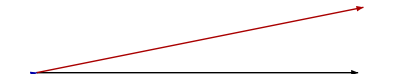

```mathematica
Graphics[{Arrow[{{0,0}, {1,0}}],{Darker@Blue, Arrow[{{0,0},{ Re[1/Zc], Im[1/Zc]}}]}, {Darker@ Red, Arrow[{{0,0}, {Re[vs/(69 10^3/ Sqrt[3])], Im[vs/(69 10^3/ Sqrt[3])]}}]}}]
```

```mathematica
(Arg[vs] - Arg[is])/π 180
```

-10.7923

```mathematica
vs/(69 10^3/Sqrt[3])
```

1.01651+0.134115 ⅈ

Empregando o condutor Drake

```mathematica
rc =  Sqrt[795 10^3 MCM/π]
```

11.3237

```mathematica
z=0.0818 + 0.4514  I;
y= 3.6860  10^(-6) I;
```

```mathematica
Zc= Sqrt[z/y]
```

351.37-31.5794 ⅈ

```mathematica
γ= Sqrt[z y];
a= Cosh[γ ℓ];
c= 1/Zc Sinh[γ ℓ];
```

```mathematica
Q={{a,b},{c,a}};
MatrixForm[Q]
```

(0.99468+0.000963136 ⅈ | 15.2579+38.6463 ⅈ
-9.47371×10^-8+0.000294357 ⅈ | 0.99468+0.000963136 ⅈ)

```mathematica
Pn = Re[ Vn^2/Zc]/ 10^6 (* pot nominal em MW *)
```

13.4413

```mathematica
Det[Q]
```

1.+2.77556×10^-17 ⅈ

```mathematica
Vr = 138. 10^3/Sqrt[3]
```

79674.3

## Aumento do carregamento

Supondo uma tensão no terminal receptor igual a 1 pu, mas com o dobro da corrente, calcule a tensão no terminal emissor e as perdas no circuito

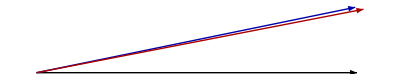

```mathematica
(* 
Graphics[{Arrow[{{0,0}, {1,0}}],{Darker@Blue, Arrow[{{0,0},{ Re[is], Im[is]}}]}, {Darker@ Red, Arrow[{{0,0}, {Re[vs], Im[vs]}}]}}]
*)
```

## Carregamento sem fator de potência unitário

Considerando, que a carga no terminal receptor tem a parte real dada por Re[Zc] e fator de potência de 0,95 atrasado, obtenha a tensão no terminal emissor

Repita o procedimento supondo fator de potência de 0,95 adiantado